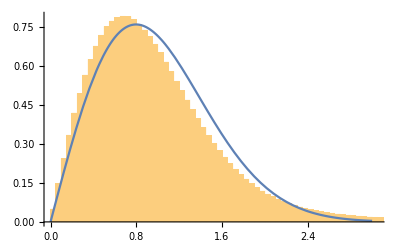

```mathematica
Clear["Global`*"]
n = 10000;
eglist = Table[Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[1000]]],{i,1,n}];
egspace = Table[Differences[Sort[eglist [[i]]]],{i,1,n}]//Flatten;
norms = egspace/Mean[egspace];
p[x_] := Pi×x/2×Exp[-Pi×x^2/4];
Show[{Histogram[norms,{0.05},"PDF"],Plot[p[x],{x,0,3}]}]
```

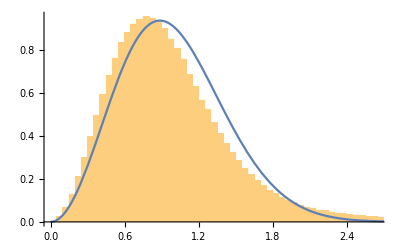

```mathematica
Clear["Global`*"]
n = 1000;
eglist = Table[Eigenvalues[RandomVariate[GaussianUnitaryMatrixDistribution[1000]]],{i,1,n}];
egspace = Table[Differences[Sort[eglist [[i]]]],{i,1,n}]//Flatten;
norms = egspace/Mean[egspace];
p[x_] := (32/(Pi)^2)x^2×Exp[-4/Pi×x^2];
Show[{Histogram[norms,{0.05},"PDF"],Plot[p[x],{x,0,3}]}]
```

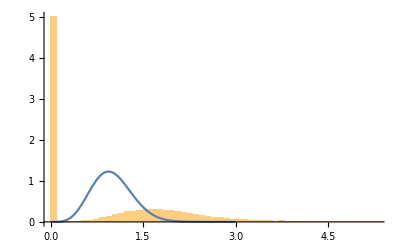

```mathematica
Clear["Global`*"]
n = 100;
eglist = Table[Eigenvalues[RandomVariate[GaussianSymplecticMatrixDistribution[1000]]],{i,1,n}];
egspace = Table[Differences[Sort[eglist [[i]]]],{i,1,n}]//Flatten;
norms = egspace/Mean[egspace];
p[x_] := (64/(9×Pi))^3×x^4×Exp[-64/(9×Pi)×x^2];
Show[{Histogram[norms,{0.1},"PDF"],Plot[p[x],{x,0,3}]}]
```